```mathematica
ene={-1.3373203592411151,-0.18643394354763032,-0.07105746396493018,-0.0374071689315123,-0.023050971893692207,-0.01561839010970445,-0.011277794810933273,-0.008524333099639847,-0.006668809747345961,-0.005359292725220399,-0.004400800927001569,-0.0036782198975480185,-0.0031200305071230616,-0.002679897830738298,-0.002326732427661682,-0.0020390440573301305,-0.0018015927229981799,-0.0016033276090361426,-0.0014360775387558533,-0.0012936952585533845}
```

{-1.33732,-0.186434,-0.0710575,-0.0374072,-0.023051,-0.0156184,-0.0112778,-0.00852433,-0.00666881,-0.00535929,-0.0044008,-0.00367822,-0.00312003,-0.0026799,-0.00232673,-0.00203904,-0.00180159,-0.00160333,-0.00143608,-0.0012937}

```mathematica
ClearAll@c;
c=First[c/.Solve[(-1/(2 n^2)+c/(√π n^3)==-0.0012936952585533845)/.n->20,c]]
```

-0.619583

```mathematica
ϵ=Flatten[Table[-1/(2 n^2)+c/(√π n^3),{n,20}][[#]]&/@Range@20]
```

{-0.849562,-0.168695,-0.0685023,-0.0367119,-0.0227965,-0.0155072,-0.0112232,-0.00849524,-0.00665235,-0.00534956,-0.00439486,-0.00367452,-0.00311769,-0.00267841,-0.0023258,-0.00203847,-0.00180125,-0.00160315,-0.00143601,-0.0012937}

```mathematica
δϵ =Table[Abs[(ϵ[[i]]-ene[[i]])/ene[[i]]],{i,20}]
```

{0.364728,0.0951473,0.0359591,0.0185863,0.0110397,0.00711714,0.00483976,0.00341313,0.00246839,0.00181566,0.00134938,0.00100723,0.000750573,0.000554498,0.000402392,0.000282856,0.000187881,0.000111709,0.0000501286,0.}

```mathematica
Lδϵ={-ene[[#]],δϵ[[#]]}&/@Range@20
```

{{1.33732,0.364728},{0.186434,0.0951473},{0.0710575,0.0359591},{0.0374072,0.0185863},{0.023051,0.0110397},{0.0156184,0.00711714},{0.0112778,0.00483976},{0.00852433,0.00341313},{0.00666881,0.00246839},{0.00535929,0.00181566},{0.0044008,0.00134938},{0.00367822,0.00100723},{0.00312003,0.000750573},{0.0026799,0.000554498},{0.00232673,0.000402392},{0.00203904,0.000282856},{0.00180159,0.000187881},{0.00160333,0.000111709},{0.00143608,0.0000501286},{0.0012937,0.}}

```mathematica
δE=Join[Table[Abs[(-1/(2 i^2)-ene[[i]])/ene[[i]]],{i,20}]]
```

{0.626118,0.329521,0.21816,0.164599,0.132358,0.110735,0.095206,0.083506,0.0743716,0.0670411,0.0610274,0.0560047,0.0517465,0.0480904,0.0449172,0.0421369,0.039681,0.0374956,0.0355385,0.0337755}

```mathematica
LδE={-ene[[#]],δE[[#]]}&/@Range@20
```

{{1.33732,0.626118},{0.186434,0.329521},{0.0710575,0.21816},{0.0374072,0.164599},{0.023051,0.132358},{0.0156184,0.110735},{0.0112778,0.095206},{0.00852433,0.083506},{0.00666881,0.0743716},{0.00535929,0.0670411},{0.0044008,0.0610274},{0.00367822,0.0560047},{0.00312003,0.0517465},{0.0026799,0.0480904},{0.00232673,0.0449172},{0.00203904,0.0421369},{0.00180159,0.039681},{0.00160333,0.0374956},{0.00143608,0.0355385},{0.0012937,0.0337755}}

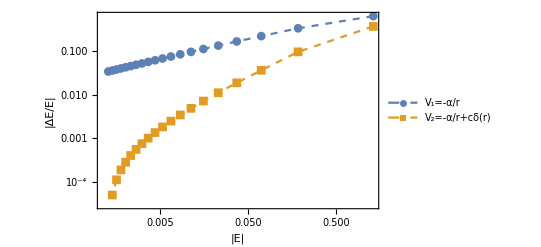

```mathematica
ListLogLogPlot[{LδE,Lδϵ},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->Reverse[{"|ΔE/E|","|E|"}],RotateLabel->False,ImageSize->Full,PlotStyle->Dashed,PlotLegends->{"V_1=-α/r","V_2=-α/r+cδ(r)"}]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\LepageFigure_1.eps",%];
```